# Symmetrized covariant derivatives

In this notebook I’ll try to develop a (reasonably) fast implementation of symmetrized covariant derivatives.

Teake Nutma

```mathematica
DateString[]
```

Sun 2 Feb 2014 22:16:18

## Introduction

### Notation

With a symmetrized n-fold covariant derivative I simply mean the symmetrization of n covariant derivatives. The notation is as follows:

∇_(a_1... a_n) = ∇_((a_1) ∇_a_2... ∇_(a_(n-1)) ∇_(a_n))

Because it is always possible to commute adjacent covariant derivatives by introducing curvature, a symmetrized covariant derivative can in general be expressed as

∇_(a_1... a_n) = ∇_a_1 ...∇_a_n + polynomial in Riemanns

or vice-versa:

∇_a_1 ... ∇_a_n=  ∇_(a_1... a_n) - polynomial in Riemanns

In principle the polynomial can also include torsion, but I’ll ignore that in this discussion.
For example, we have

∇_(ab) T^c= 1/2(∇_a ∇_b +∇_b ∇_a)T^c
		= 1/2(∇_a ∇_b +∇_a ∇_b +∇_b ∇_a -∇_a ∇_b)T^c
		= (∇_a ∇_b +1/2[∇_b,∇_a])T^c
		= (∇_a ∇_b δ_d^c+1/2 R_abd^c)T^d

or vice-versa:

∇_ab T^c= ∇_((a) ∇_(b)) T^c-1/2 R_abd^c T^d

### Benefits

The benefit of symmetrizing covariant derivatives mainly lies in canonicalizing. xTensor’s canonicalizer makes no attempt to scan for symmetries in covariant derivatives, and for example doesn’t know that

F^[ab]∇_a ∇_b ϕ = 0

xTensor does include the function SortCovDs, but that sorts derivatives in an ad-hoc manner without taking the nature of the indices into account (frees, dummies, etc). Using SortCovDs on the above equation still won’t reproduce zero.

Explicitly going to a basis where all derivatives are symmetrized solves these issues.

Additionally, symmetrizing covariant derivatives is needed when implementing Bianchi identities on second and higher order derivatives of the Riemann tensor.

### Properties

Distributivity is inherited from the ‘ordinary’ derivative:

∇_(a_1... a_n) (X+Y)= ∇_(a_1... a_n) X+∇_(a_1... a_n) Y

If the ordinary derivative is Leibniz, we have:

∇_(a_1... a_n) (X Y)= ∑_(i=0)^n (n
i)∇_(((a_1... a_i)) X  ∇_((a_(i+1)... a_n))) Y

A consistency check on this formula is counting the number of terms on boths sides; the l.h.s. has 2^n terms, the same as the r.h.s: ∑_(i=0)^n (n
i)=2^n.

Integrating by parts also carries over nicely:

Y ∇_(a_1... a_n) X=(-1)^n  X ∇_(a_1... a_n) Y+ total derivative

It is reasonably straightforward to deduce a semi-closed formula for a symmetrized derivative eating up one ordinary on the right. It reads

∇_(a_1... a_n) ∇_b=∇_(a_1... a_n b) -∑_(i=1)^n i/(n+1)∇_(((a_1... a_(i-1))) [∇_b,∇_a_i] ∇_((a_(i+1)... a_n)))

where the symmetrization in the sum on the r.h.s. is over the a indices (thus excluding b).
Likewise, there is a semi-closed formula for eating a single derivative on the left:

∇_b ∇_(a_1... a_n)=∇_(a_1... a_n b) -∑_(i=1)^n (n+1-i)/(n+1)∇_(((a_1... a_(i-1))) [∇_a_i,∇_b] ∇_((a_(i+1)... a_n)))

These formulas are semi-closed because their right-hand-sides contain terms of the form

∇_(a_1... a_n) ∇_(b_1... b_m)

for which I don’t have a closed formula expressing it in terms of ∇_(a_1... a_n b_1... b_m) .
So the current approach to symmetrizing the above expression is to do it recursively: first break of one derivative as follows,

∇_(a_1... a_n) ∇_(b_1... b_m)=1/m(∇_(a_1... a_n) ∇_b_1 ∇_(b_2... b_m) + permutations),

then use the semi-closed formula on ∇_(a_1... a_n) ∇_b_1, and repeat. This is not very efficient.

Rewriting (11) using the Leibniz property (8) and writing out the commutator improves things a bit, because we can then use the fact that

∇_(((a_1... a_n)) ∇_((b_1... b_m)))=∇_(a_1... a_n b_1... b_m)

But unfortunately we still encounter terms like

(R_(b (a_i a_(i+1)))^d∇_(a_(j+1)... a_(i-1)) ∇_((a_(i+2)... a_n)d))

with a symmetrization over all a indices, which is not equal to (R_(b (a_i a_(i+1)))^d∇_((a_(j+1)... a_(i-1)a_(i+2)... a_n)d)). So at the moment I’m using the recursive approach.

## Examples

This section only evaluates properly after the “Implementation” section below has been evaluated.

```mathematica
?SymmetrizeCovDs
```

SymmetrizeCovDs[expr] converts all covariant derivatives in expr into symmetrized covariant derivatives by commuting them. SymmetrizeCovDs[expr, cd] only convert the covariant derivative cd.

```mathematica
CD[-a]@CD[-b]@T1[c]
%//SymmetrizeCovDs
%//ToCanonical
```

▽_a▽_b T1 | c

-1/2 R[▽] |   |   |   | c
a | b | d |   T1 | d
 +▽_(ba)^T1 | c

1/2 R[▽] |   |   | c |  
a | b |   | d T1 | d
 +▽_(ab)^T1 | c

```mathematica
RiemannCD[a,b,c,d]CD[-c]@CD[-d]@T0[]
%//ToCanonical
%//SymmetrizeCovDs
%//ToCanonical
```

R[▽] | a | b | c | d
  |   |   |   (▽_c▽_d T0)

-R[▽] | a | b | c | d
  |   |   |   (▽_d▽_c T0)

-R[▽] | a | b | c | d
  |   |   |   (▽_(cd)^T0)

0

```mathematica
metric[-d,-f]CD[a,b]@RiemannCD[c,d,e,f]
%//ContractMetric//ToCanonical
```

g |   |  
d | f (▽_^(ab)R[▽] | c | d | e | f
  |   |   |  )

▽_^(ab)R[▽] | c | e
  |

```mathematica
?ExpandSymCovDs
```

ExpandSymCovDs[expr] expands all symmetric covariant derivatives in terms of ordinary ones.ExpandSymCovDs[expr,cd] expands only symmetric covariant derivatives associated to the covariant derivative cd.

```mathematica
CD[c]@CD[b]@CD[a]@RicciCD[d,e]
%//SymmetrizeCovDs//ToCanonical
%//ExpandSymCovDs//SortCovDs//ToCanonical
```

▽^c▽^b▽^a R[▽] | d | e
  |

-1/2 R[▽] | b | c | e | f
  |   |   |   (▽^a R[▽] | d |  
  | f)-1/2 R[▽] | b | c | d | f
  |   |   |   (▽^a R[▽] | e |  
  | f)-1/2 R[▽] | a | c | e | f
  |   |   |   (▽^b R[▽] | d |  
  | f)-1/2 R[▽] | a | c | d | f
  |   |   |   (▽^b R[▽] | e |  
  | f)-1/3 R[▽] | e | f
  |   (▽^b R[▽] | a | c | d |  
  |   |   | f)-1/3 R[▽] | d | f
  |   (▽^b R[▽] | a | c | e |  
  |   |   | f)-1/2 R[▽] | a | b | e | f
  |   |   |   (▽^c R[▽] | d |  
  | f)-1/2 R[▽] | a | b | d | f
  |   |   |   (▽^c R[▽] | e |  
  | f)-1/3 R[▽] | e | f
  |   (▽^c R[▽] | a | b | d |  
  |   |   | f)-1/3 R[▽] | d | f
  |   (▽^c R[▽] | a | b | e |  
  |   |   | f)-1/6 R[▽] | a | b | c | f
  |   |   |   (▽_f R[▽] | d | e
  |  )-1/6 R[▽] | a | c | b | f
  |   |   |   (▽_f R[▽] | d | e
  |  )-1/2 R[▽] | a | f | b | c
  |   |   |   (▽_f R[▽] | d | e
  |  )+▽_^(abc)R[▽] | d | e
  |

▽^c▽^b▽^a R[▽] | d | e
  |

## Implementation

### Package, manifold, metric, and tensors

```mathematica
<<xAct`xTras`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.0, {2013,1,27}

CopyRight (C) 2003-2013, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.0.5, {2013,1,30}

CopyRight (C) 2002-2013, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xPert`  version 1.0.3, {2013,1,27}

CopyRight (C) 2005-2013, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

** DefInertHead: Defining inert head Perturbation.

------------------------------------------------------------

Package xAct`Invar`  version 2.0.4, {2013,1,27}

CopyRight (C) 2006-2013, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.0, {2013,1,30}

CopyRight (C) 2005-2013, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.8.5, {2013,4,13}

CopyRight (C) 2011-2013, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.2.3, {2013,11,22}

CopyRight (C) 2012-2013, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
DefManifold[M,dim,IndexRange[a,l]]
```

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

```mathematica
DefMetric[-1,metric[-a,-b],CD,PrintAs->"g"]
```

** DefTensor: Defining symmetric metric tensor metric[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilonmetric[-a,-b].

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-a,-b].

** DefTensor: Defining Weyl tensor WeylCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim d

** DefCovD:  Computing RicciToTFRicci for dim d

** DefCovD:  Computing RicciToEinsteinRules for dim d

** DefTensor: Defining symmetric Schouten tensor SchoutenCD[-a,-b].

** DefTensor: Defining symmetric cosmological Schouten tensor SchoutenCCCD[LI[_],-a,-b].

** DefTensor: Defining symmetric cosmological Einstein tensor EinsteinCCCD[LI[_],-a,-b].

** DefTensor: Defining weight +2 density Detmetric[]. Determinant.

** DefParameter: Defining parameter PerturbationParametermetric.

** DefTensor: Defining tensor Perturbationmetric[LI[order],-a,-b].

Define some tensors to run tests with.

```mathematica
DefTensor[T4[a,b,c,d],M]
```

** DefTensor: Defining tensor T4[a,b,c,d].

```mathematica
DefTensor[T3[a,b,c],M]
```

** DefTensor: Defining tensor T3[a,b,c].

```mathematica
DefTensor[T1[a],M]
```

** DefTensor: Defining tensor T1[a].

```mathematica
DefTensor[T0[],M]
```

** DefTensor: Defining tensor T0[].

```mathematica
DefTensor[T2[a,b],M]
```

** DefTensor: Defining tensor T2[a,b].

```mathematica
DefTensor[S2[a,b],M,Symmetric[{a,b}]]
```

** DefTensor: Defining tensor S2[a,b].

```mathematica
DefTensor[S3[a,b,c],M,Symmetric[{a,b,c}]]
```

** DefTensor: Defining tensor S3[a,b,c].

```mathematica
DefTensor[S4[a,b,c,d],M,Symmetric[{a,b,c,d}]]
```

** DefTensor: Defining tensor S4[a,b,c,d].

### Definition of the symmetrized derivative

#### Code

The idea is to let the derivative have multiple indices, each one corresponding to  a single ‘normal’ covariant derivative. The whole of them are symmetrized over.

The symmetry group of CD is the full symmetric group:

```mathematica
SymmetryGroupOfCovD[HoldPattern[CD[inds__]]]^:=Symmetric[Range@Length@{inds}]
```

Because the number of indices is equal to the number of derivatives, CD[] is equal to the identity.

```mathematica
CD[]=Identity;
```

```mathematica
SymCovDQ[_]:=False

SymCovDQ[CD]^=True;
```

#### Tests

Test:

```mathematica
SymmetryOf[CD[a]@CD[b]@RicciScalarCD[]]
```

Symmetry[2,▽^(●2)▽^(●1)R[▽],{●1→b,●2→a},StrongGenSet[{},GenSet[]]]

```mathematica
SymmetryOf[CD[a,b]@RicciScalarCD[]]
```

Symmetry[2,▽_^(●1●2)R[▽],{●1→a,●2→b},StrongGenSet[{1,2},GenSet[Cycles[{1,2}]]]]

```mathematica
SymmetryOf[RicciCD[a,b]]
```

Symmetry[2,R[▽] | ●1 | ●2
  |  ,{●1→a,●2→b},StrongGenSet[{1,2},GenSet[Cycles[{1,2}]]]]

```mathematica
SymmetryOf[CD[e,f]@RiemannCD[a,b,c,d]]
```

Symmetry[6,▽_^(●5●6)R[▽] | ●1 | ●2 | ●3 | ●4
  |   |   |  ,{●1→a,●2→b,●3→c,●4→d,●5→e,●6→f},StrongGenSet[{1,2,3,4,5,6},GenSet[-Cycles[{1,2}],-Cycles[{3,4}],Cycles[{5,6}],Cycles[{1,3},{2,4}]]]]

```mathematica
CD[b,a]@RicciCD[d,e]-CD[a,b]@RicciCD[d,e]
%//ToCanonical
```

-(▽_^ab R[▽] | d | e
  |  )+▽_^ba R[▽] | d | e
  |

0

### Formatting

#### Code

First some helper functions.

```mathematica
AddSymBraces[{"",""}]:=
{"",""}

AddSymBraces[{downstring_,upstring_}]:=
With[
{
openbraceupQ = StringTake[downstring,1]===" ",
closebraceupQ = StringTake[downstring,-1]===" "
},
{
If[openbraceupQ," ","("]<>downstring<>If[closebraceupQ," ",")"],
If[openbraceupQ,"("," "]<>upstring<>If[closebraceupQ,")"," "]
}
];
```

```mathematica
xAct`xTensor`Private`SSSBinds[{a,b,c}]
AddSymBraces[%]
```

{   ,abc}

{     ,(abc)}

```mathematica
xAct`xTensor`Private`SSSBinds[{a}]
AddSymBraces[%]
```

{ ,a}

{   ,(a)}

The actual code. This is differs from the xTensor code by just one insertion of AddSymBraces.

```mathematica
(* Prefix notation *)
xAct`xTensor`Private`MakeBoxesCovD[der_?SymCovDQ[inds__][MBexpr_],"Prefix"]/;Length@{inds}>1:=Block[{$WarningFrom="CovD Formatting"},
xAct`xTensor`Private`FlattenRowBox@RowBox[{SubsuperscriptBox[Last@SymbolOfCovD@der,#1,#2]&@@AddSymBraces@xAct`xTensor`Private`SSSBinds[{inds}],MBexpr}]];
```

#### Tests

```mathematica
CD[a,-b,c]@RicciScalarCD[]
```

▽_b^(a c)R[▽]

```mathematica
CD[-a]@RicciScalarCD[]
```

▽_a R[▽]

```mathematica
CD[-a,-b]@RicciScalarCD[]
```

▽_(ab)^R[▽]

I’ll add proper Postfix notation later.

### Expanding

#### Code

This is the easiest bit, really.

```mathematica
ExpandSymCovDs::usage=
"ExpandSymCovDs[expr] expands all symmetric covariant derivatives in terms of ordinary ones.\
ExpandSymCovDs[expr,cd] expands only symmetric covariant derivatives associated to the covariant derivative cd.";

ExpandSymCovDs[expr_]:=
Fold[ExpandSymCovDs[#1,#2]&,expr,$CovDs];

ExpandSymCovDs[expr_,cd_?SymCovDQ]:=
expr//.HoldPattern[cd[inds__][x_]]/;Length@{inds}>1:>Symmetrize[Fold[cd[#2][#1]&,x,{inds}],{inds}];

ExpandSymCovDs[expr_,_]:=
expr;
```

#### Tests

```mathematica
CD[a,b,c,d]@RicciScalarCD[]
%//ExpandSymCovDs
```

▽_^(abcd)R[▽]

1/24 (▽^a▽^b▽^c▽^d R[▽]+▽^a▽^b▽^d▽^c R[▽]+▽^a▽^c▽^b▽^d R[▽]+▽^a▽^c▽^d▽^b R[▽]+▽^a▽^d▽^b▽^c R[▽]+▽^a▽^d▽^c▽^b R[▽]+▽^b▽^a▽^c▽^d R[▽]+▽^b▽^a▽^d▽^c R[▽]+▽^b▽^c▽^a▽^d R[▽]+▽^b▽^c▽^d▽^a R[▽]+▽^b▽^d▽^a▽^c R[▽]+▽^b▽^d▽^c▽^a R[▽]+▽^c▽^a▽^b▽^d R[▽]+▽^c▽^a▽^d▽^b R[▽]+▽^c▽^b▽^a▽^d R[▽]+▽^c▽^b▽^d▽^a R[▽]+▽^c▽^d▽^a▽^b R[▽]+▽^c▽^d▽^b▽^a R[▽]+▽^d▽^a▽^b▽^c R[▽]+▽^d▽^a▽^c▽^b R[▽]+▽^d▽^b▽^a▽^c R[▽]+▽^d▽^b▽^c▽^a R[▽]+▽^d▽^c▽^a▽^b R[▽]+▽^d▽^c▽^b▽^a R[▽])

```mathematica
CD[g,b,c]@RicciScalarCD[]
%//SymmetryOfExpression
%%//ExpandSymCovDs//Expand
%//SymmetryOfExpression
```

▽_^(gbc)R[▽]

{StrongGenSet[{1,2},GenSet[Cycles[{2,3}],Cycles[{1,2}]]],{b,c,g}}

1/6 (▽^b▽^c▽^g R[▽])+1/6 (▽^b▽^g▽^c R[▽])+1/6 (▽^c▽^b▽^g R[▽])+1/6 (▽^c▽^g▽^b R[▽])+1/6 (▽^g▽^b▽^c R[▽])+1/6 (▽^g▽^c▽^b R[▽])

{StrongGenSet[{1,2},GenSet[Cycles[{2,3}],Cycles[{1,2}]]],{b,c,g}}

```mathematica
CD[g,b,c]@RicciScalarCD[]
%//ExpandSymCovDs[#,CD]&
%%//ExpandSymCovDs[#,PD]&
```

▽_^(gbc)R[▽]

1/6 (▽^b▽^c▽^g R[▽]+▽^b▽^g▽^c R[▽]+▽^c▽^b▽^g R[▽]+▽^c▽^g▽^b R[▽]+▽^g▽^b▽^c R[▽]+▽^g▽^c▽^b R[▽])

▽_^(gbc)R[▽]

```mathematica
CD[a]@CD[b,c]@T1[d]//ExpandSymCovDs
```

1/2 (▽^a▽^b▽^c T1 | d
 +▽^a▽^c▽^b T1 | d
 )

### Unordered Partitioned Permutations

#### Theory

We need a fast way to fully symmetrize expressions of the form (S^1)_(a_1... a_i_1)(S^2)_(a_(1+i_1)... a_(i_1+i_2))... (S^n)_(a_(1+i_1+i_2+...+i_(n-1))... a_(i_1+i_2+ ... i_n))  where the S’s are symmetric tensors and {i_1,...,i_n} is an integer partition of p=∑_(j=1)^n i_j, the total number of indices. The naive way is to fully symmetrize all indices, and the canonicalize them. For example:

```mathematica
S2[a,b]S3[c,d,e]//Symmetrize//ToCanonical//AbsoluteTiming
```

{0.47601,1/10 S2 | d | e
  |   S3 | a | b | c
  |   |  +1/10 S2 | c | e
  |   S3 | a | b | d
  |   |  +1/10 S2 | c | d
  |   S3 | a | b | e
  |   |  +1/10 S2 | b | e
  |   S3 | a | c | d
  |   |  +1/10 S2 | b | d
  |   S3 | a | c | e
  |   |  +1/10 S2 | b | c
  |   S3 | a | d | e
  |   |  +1/10 S2 | a | e
  |   S3 | b | c | d
  |   |  +1/10 S2 | a | d
  |   S3 | b | c | e
  |   |  +1/10 S2 | a | c
  |   S3 | b | d | e
  |   |  +1/10 S2 | a | b
  |   S3 | c | d | e
  |   |  }

```mathematica
T1[a]S4[b,c,d,e]//Symmetrize//ToCanonical//AbsoluteTiming
```

{0.48382,1/5 S4 | b | c | d | e
  |   |   |   T1 | a
 +1/5 S4 | a | c | d | e
  |   |   |   T1 | b
 +1/5 S4 | a | b | d | e
  |   |   |   T1 | c
 +1/5 S4 | a | b | c | e
  |   |   |   T1 | d
 +1/5 S4 | a | b | c | d
  |   |   |   T1 | e
 }

But this becomes excruciatingly slow for large p, even though there are ‘only’ (p!)/(i_1!  ... i_n!) terms.
A better way is to first enumerate all possible terms for a given integer partition. This is what UnorderedPartitionedPermutations does.

#### Code

```mathematica
ClearAll[UnorderedPartitionedPermutations];

UnorderedPartitionedPermutations::usage=
"UnorderedPartitionedPermutations[list, partition] gives all permutations of list whose sub-parts according the partition are unordered. For example, UnorderedPartitionedPermutations[list,Table[1,{Length@list}]] gives all ordinary permutations of list, and UnorderedPartitionedPermutations[list,{Length@list}] returns the list itself.";

(* The general case: do a recursion into the partition. The workhorse is Subsets. *)
UnorderedPartitionedPermutations[set_List,partition:{i1_Integer,rest__Integer}]/;Total@partition===Length@set:=
Flatten[
Function[subset,
Map[
Join[{subset},#]&,
UnorderedPartitionedPermutations[Complement[set,subset],{rest}]
]]/@Subsets[set,{i1}],
1
]

(* The limiting case where the partition is just one number. *)
UnorderedPartitionedPermutations[set_List,partition:{i1_Integer}]/;Total@partition===Length@set:=
{{set}}

(* The limiting case where both the partition and the set are empty. *)
UnorderedPartitionedPermutations[{},{}]:=
{};

Protect[UnorderedPartitionedPermutations];
```

```mathematica
PartitionedSymmetrize[f_Function,indices:(List|IndexList)[___],partition:{___Integer}]/;Total@partition===Length@indices:=
With[{fseq=f/.s_Slot:>Sequence@@s},
Times@@(partition!)/Total[partition]!  Total[fseq@@#&/@UnorderedPartitionedPermutations[indices,partition]]
];
```

#### Tests

```mathematica
UnorderedPartitionedPermutations[Range@4,{4}]
```

{{{1,2,3,4}}}

```mathematica
UnorderedPartitionedPermutations[Range@4,Table[1,{4}]]
Flatten/@%===Permutations[Range@4]
```

{{{1},{2},{3},{4}},{{1},{2},{4},{3}},{{1},{3},{2},{4}},{{1},{3},{4},{2}},{{1},{4},{2},{3}},{{1},{4},{3},{2}},{{2},{1},{3},{4}},{{2},{1},{4},{3}},{{2},{3},{1},{4}},{{2},{3},{4},{1}},{{2},{4},{1},{3}},{{2},{4},{3},{1}},{{3},{1},{2},{4}},{{3},{1},{4},{2}},{{3},{2},{1},{4}},{{3},{2},{4},{1}},{{3},{4},{1},{2}},{{3},{4},{2},{1}},{{4},{1},{2},{3}},{{4},{1},{3},{2}},{{4},{2},{1},{3}},{{4},{2},{3},{1}},{{4},{3},{1},{2}},{{4},{3},{2},{1}}}

True

```mathematica
Flatten/@UnorderedPartitionedPermutations[Range@8,Table[1,{8}]]===Permutations[Range@8]
```

True

```mathematica
UnorderedPartitionedPermutations[{a,b,c},{1,2}]//TableForm[#,TableDepth->1]&
```

{{a},{b,c}}
{{b},{a,c}}
{{c},{a,b}}

```mathematica
UnorderedPartitionedPermutations[{a,b,c},{2,1}]//TableForm[#,TableDepth->1]&
```

{{a,b},{c}}
{{a,c},{b}}
{{b,c},{a}}

```mathematica
Table[RandomInteger[{1,5}],{3}]
Total[%]!/(Times@@(%!))
UnorderedPartitionedPermutations[Range@Total[%%],%%];
Union[%]//Length
Union@Map[Length,%%,{2}]
```

{3,1,4}

280

280

{{3,1,4}}

```mathematica
PartitionedSymmetrize[S2[#1]S3[#2]&,{a,b,c,d,e},{2,3}]//Expand//AbsoluteTiming
S2[a,b]S3[c,d,e]//Symmetrize//ToCanonical//AbsoluteTiming
%%-%
```

{0.00062,1/10 S2 | d | e
  |   S3 | a | b | c
  |   |  +1/10 S2 | c | e
  |   S3 | a | b | d
  |   |  +1/10 S2 | c | d
  |   S3 | a | b | e
  |   |  +1/10 S2 | b | e
  |   S3 | a | c | d
  |   |  +1/10 S2 | b | d
  |   S3 | a | c | e
  |   |  +1/10 S2 | b | c
  |   S3 | a | d | e
  |   |  +1/10 S2 | a | e
  |   S3 | b | c | d
  |   |  +1/10 S2 | a | d
  |   S3 | b | c | e
  |   |  +1/10 S2 | a | c
  |   S3 | b | d | e
  |   |  +1/10 S2 | a | b
  |   S3 | c | d | e
  |   |  }

{0.46734,1/10 S2 | d | e
  |   S3 | a | b | c
  |   |  +1/10 S2 | c | e
  |   S3 | a | b | d
  |   |  +1/10 S2 | c | d
  |   S3 | a | b | e
  |   |  +1/10 S2 | b | e
  |   S3 | a | c | d
  |   |  +1/10 S2 | b | d
  |   S3 | a | c | e
  |   |  +1/10 S2 | b | c
  |   S3 | a | d | e
  |   |  +1/10 S2 | a | e
  |   S3 | b | c | d
  |   |  +1/10 S2 | a | d
  |   S3 | b | c | e
  |   |  +1/10 S2 | a | c
  |   S3 | b | d | e
  |   |  +1/10 S2 | a | b
  |   S3 | c | d | e
  |   |  }

{-0.46672,0}

```mathematica
PartitionedSymmetrize[T1[#1]S4[#2]&,{a,b,c,d,e},{1,4}]//Expand//AbsoluteTiming
T1[a]S4[b,c,d,e]//Symmetrize//ToCanonical//AbsoluteTiming
%%-%
```

{0.00047,1/5 S4 | b | c | d | e
  |   |   |   T1 | a
 +1/5 S4 | a | c | d | e
  |   |   |   T1 | b
 +1/5 S4 | a | b | d | e
  |   |   |   T1 | c
 +1/5 S4 | a | b | c | e
  |   |   |   T1 | d
 +1/5 S4 | a | b | c | d
  |   |   |   T1 | e
 }

{0.4858,1/5 S4 | b | c | d | e
  |   |   |   T1 | a
 +1/5 S4 | a | c | d | e
  |   |   |   T1 | b
 +1/5 S4 | a | b | d | e
  |   |   |   T1 | c
 +1/5 S4 | a | b | c | e
  |   |   |   T1 | d
 +1/5 S4 | a | b | c | d
  |   |   |   T1 | e
 }

{-0.48533,0}

```mathematica
PartitionedSymmetrize[S2[#1]T1[#2]S3[#3]&,{a,b,c,d,e,f},{2,1,3}]//Expand//AbsoluteTiming;
S2[a,b]T1[c]S3[d,e,f]//Symmetrize//ToCanonical//AbsoluteTiming;
%%-%
```

{-3.26436,0}

### Distributivity and Leibniz and stuff

#### Code

These definitions should be attached to CD at definition time.

```mathematica
(* Map over lists. *)
HoldPattern[CD[inds__][x_List]]:=
CD[inds]/@x;
```

```mathematica
(* Map over sums. *)
HoldPattern[CD[inds__][x_Plus]]:=
CD[inds]/@x;
```

```mathematica
(* Action on constants. *)
HoldPattern[CD[inds__][x_?ConstantQ * y_]]:=
x CD[inds][y];

HoldPattern[CD[__][_?ConstantQ]]:=
0;
```

```mathematica
(* Main function on products of two expressions. *)
HoldPattern[CD[inds__][x_*y_]]:=
Module[
{i,l=Length@{inds}}
,
Sum[
Binomial[l,i]PartitionedSymmetrize[CD[#1][x]CD[#2][y]&,{inds},{i,l-i}]
,
{i,0,l} 
]
];
```

```mathematica
HoldPattern[CD[inds__][x_^y_]]:=
Block[{Keep},
CD[inds][Keep[x]x^(y-1)]/.Keep->Sequence
];
```

```mathematica
HoldPattern[CD[inds__][Scalar[x_]]]:=
CD[inds][ReplaceDummies[x]];
```

```mathematica
(* Only do this is CD is metric compatible. *)
HoldPattern[CD[__][metric[__]]]=
0;
```

#### Tests

```mathematica
CD[a,b,c]@{metric[d,e],RicciCD[d,e]}
```

{0,▽_^(abc)R[▽] | d | e
  |  }

```mathematica
CD[a][Scalar[RicciCD[a,b]RicciCD[-a,-b]]^2]
```

2 (R[▽] |   |  
a | b R[▽] | a | b
  |  ) (R[▽] | b | c
  |   (▽^a R[▽] |   |  
b | c)+R[▽] |   |  
b | c (▽^a R[▽] | b | c
  |  ))

```mathematica
CD[a,b][Scalar[RicciCD[a,b]RicciCD[-a,-b]]^2]
CD[a]@CD[b][Scalar[RicciCD[a,b]RicciCD[-a,-b]]^2]//Symmetrize[#,{a,b}]&;
%-%%//ExpandSymCovDs//ToCanonical
```

(R[▽] | e | f
  |   (▽^a R[▽] |   |  
e | f)+R[▽] |   |  
e | f (▽^a R[▽] | e | f
  |  )) (R[▽] | c | d
  |   (▽^b R[▽] |   |  
c | d)+R[▽] |   |  
c | d (▽^b R[▽] | c | d
  |  ))+(R[▽] | c | d
  |   (▽^a R[▽] |   |  
c | d)+R[▽] |   |  
c | d (▽^a R[▽] | c | d
  |  )) (R[▽] | e | f
  |   (▽^b R[▽] |   |  
e | f)+R[▽] |   |  
e | f (▽^b R[▽] | e | f
  |  ))+2 (R[▽] |   |  
a | b R[▽] | a | b
  |  ) ((▽^a R[▽] | c | d
  |  ) (▽^b R[▽] |   |  
c | d)+(▽^a R[▽] |   |  
c | d) (▽^b R[▽] | c | d
  |  )+R[▽] | c | d
  |   (▽_^(ab)R[▽] |   |  
c | d)+R[▽] |   |  
c | d (▽_^(ab)R[▽] | c | d
  |  ))

0

```mathematica
CD[a,b][  RicciScalarCD[] +RicciScalarCD[]^2]
%//ExpandSymCovDs//ToCanonical;
CD[a]@CD[b][RicciScalarCD[]+RicciScalarCD[]^2]//Symmetrize[#,{a,b}]&;
%%-%//ToCanonical
```

2 (▽^a R[▽]) (▽^b R[▽])+▽_^(ab)R[▽]+2 R[▽] (▽_^(ab)R[▽])

0

```mathematica
CD[a,b][-45 RicciScalarCD[]]
```

-45 (▽_^(ab)R[▽])

```mathematica
CD[a,b][RicciScalarCD[]RicciCD[c,d]]//ToCanonical
%//ExpandSymCovDs//ToCanonical;
CD[a]@CD[b][RicciScalarCD[]RicciCD[c,d]]//Symmetrize[#,{a,b}]&;
%%-%//ToCanonical
```

(▽^a R[▽]) (▽^b R[▽] | c | d
  |  )+(▽^a R[▽] | c | d
  |  ) (▽^b R[▽])+R[▽] (▽_^(ab)R[▽] | c | d
  |  )+R[▽] | c | d
  |   (▽_^(ab)R[▽])

0

```mathematica
CD[a,b,e][RicciScalarCD[]RicciCD[c,d]]//ToCanonical
%//ExpandSymCovDs;
CD[a]@CD[b]@CD[e][RicciScalarCD[]RicciCD[c,d]]//Symmetrize[#,{a,b,e}]&;
%%-%//ToCanonical
```

(▽^e R[▽]) (▽_^(ab)R[▽] | c | d
  |  )+(▽^e R[▽] | c | d
  |  ) (▽_^(ab)R[▽])+(▽^b R[▽]) (▽_^(ae)R[▽] | c | d
  |  )+(▽^b R[▽] | c | d
  |  ) (▽_^(ae)R[▽])+(▽^a R[▽]) (▽_^(be)R[▽] | c | d
  |  )+(▽^a R[▽] | c | d
  |  ) (▽_^(be)R[▽])+R[▽] (▽_^(abe)R[▽] | c | d
  |  )+R[▽] | c | d
  |   (▽_^(abe)R[▽])

0

```mathematica
CD[a,b,c,d,e,f][RiemannCD[g,h,i,j]RicciCD[k,l]]//ToCanonical
%//ExpandSymCovDs;
CD[a]@CD[b]@CD[c]@CD[d]@CD[e]@CD[f][RiemannCD[g,h,i,j]RicciCD[k,l]]//Symmetrize[#,{a,b,c,d,e,f}]&;
%%-%//ToCanonical
```

(▽_^(aef)R[▽] | g | h | i | j
  |   |   |  ) (▽_^(bcd)R[▽] | k | l
  |  )+(▽_^(aef)R[▽] | k | l
  |  ) (▽_^(bcd)R[▽] | g | h | i | j
  |   |   |  )+(▽_^(adf)R[▽] | g | h | i | j
  |   |   |  ) (▽_^(bce)R[▽] | k | l
  |  )+(▽_^(adf)R[▽] | k | l
  |  ) (▽_^(bce)R[▽] | g | h | i | j
  |   |   |  )+(▽_^(ade)R[▽] | g | h | i | j
  |   |   |  ) (▽_^(bcf)R[▽] | k | l
  |  )+(▽_^(ade)R[▽] | k | l
  |  ) (▽_^(bcf)R[▽] | g | h | i | j
  |   |   |  )+(▽_^(acf)R[▽] | g | h | i | j
  |   |   |  ) (▽_^(bde)R[▽] | k | l
  |  )+(▽_^(acf)R[▽] | k | l
  |  ) (▽_^(bde)R[▽] | g | h | i | j
  |   |   |  )+(▽_^(ace)R[▽] | g | h | i | j
  |   |   |  ) (▽_^(bdf)R[▽] | k | l
  |  )+(▽_^(ace)R[▽] | k | l
  |  ) (▽_^(bdf)R[▽] | g | h | i | j
  |   |   |  )+(▽_^(acd)R[▽] | g | h | i | j
  |   |   |  ) (▽_^(bef)R[▽] | k | l
  |  )+(▽_^(acd)R[▽] | k | l
  |  ) (▽_^(bef)R[▽] | g | h | i | j
  |   |   |  )+(▽_^(abf)R[▽] | g | h | i | j
  |   |   |  ) (▽_^(cde)R[▽] | k | l
  |  )+(▽_^(abf)R[▽] | k | l
  |  ) (▽_^(cde)R[▽] | g | h | i | j
  |   |   |  )+(▽_^(abe)R[▽] | g | h | i | j
  |   |   |  ) (▽_^(cdf)R[▽] | k | l
  |  )+(▽_^(abe)R[▽] | k | l
  |  ) (▽_^(cdf)R[▽] | g | h | i | j
  |   |   |  )+(▽_^(abd)R[▽] | g | h | i | j
  |   |   |  ) (▽_^(cef)R[▽] | k | l
  |  )+(▽_^(abd)R[▽] | k | l
  |  ) (▽_^(cef)R[▽] | g | h | i | j
  |   |   |  )+(▽_^(abc)R[▽] | g | h | i | j
  |   |   |  ) (▽_^(def)R[▽] | k | l
  |  )+(▽_^(abc)R[▽] | k | l
  |  ) (▽_^(def)R[▽] | g | h | i | j
  |   |   |  )+(▽_^(ef)R[▽] | g | h | i | j
  |   |   |  ) (▽_^(abcd)R[▽] | k | l
  |  )+(▽_^(ef)R[▽] | k | l
  |  ) (▽_^(abcd)R[▽] | g | h | i | j
  |   |   |  )+(▽_^(df)R[▽] | g | h | i | j
  |   |   |  ) (▽_^(abce)R[▽] | k | l
  |  )+(▽_^(df)R[▽] | k | l
  |  ) (▽_^(abce)R[▽] | g | h | i | j
  |   |   |  )+(▽_^(de)R[▽] | g | h | i | j
  |   |   |  ) (▽_^(abcf)R[▽] | k | l
  |  )+(▽_^(de)R[▽] | k | l
  |  ) (▽_^(abcf)R[▽] | g | h | i | j
  |   |   |  )+(▽_^(cf)R[▽] | g | h | i | j
  |   |   |  ) (▽_^(abde)R[▽] | k | l
  |  )+(▽_^(cf)R[▽] | k | l
  |  ) (▽_^(abde)R[▽] | g | h | i | j
  |   |   |  )+(▽_^(ce)R[▽] | g | h | i | j
  |   |   |  ) (▽_^(abdf)R[▽] | k | l
  |  )+(▽_^(ce)R[▽] | k | l
  |  ) (▽_^(abdf)R[▽] | g | h | i | j
  |   |   |  )+(▽_^(cd)R[▽] | g | h | i | j
  |   |   |  ) (▽_^(abef)R[▽] | k | l
  |  )+(▽_^(cd)R[▽] | k | l
  |  ) (▽_^(abef)R[▽] | g | h | i | j
  |   |   |  )+(▽_^(bf)R[▽] | g | h | i | j
  |   |   |  ) (▽_^(acde)R[▽] | k | l
  |  )+(▽_^(bf)R[▽] | k | l
  |  ) (▽_^(acde)R[▽] | g | h | i | j
  |   |   |  )+(▽_^(be)R[▽] | g | h | i | j
  |   |   |  ) (▽_^(acdf)R[▽] | k | l
  |  )+(▽_^(be)R[▽] | k | l
  |  ) (▽_^(acdf)R[▽] | g | h | i | j
  |   |   |  )+(▽_^(bd)R[▽] | g | h | i | j
  |   |   |  ) (▽_^(acef)R[▽] | k | l
  |  )+(▽_^(bd)R[▽] | k | l
  |  ) (▽_^(acef)R[▽] | g | h | i | j
  |   |   |  )+(▽_^(bc)R[▽] | g | h | i | j
  |   |   |  ) (▽_^(adef)R[▽] | k | l
  |  )+(▽_^(bc)R[▽] | k | l
  |  ) (▽_^(adef)R[▽] | g | h | i | j
  |   |   |  )+(▽_^(af)R[▽] | g | h | i | j
  |   |   |  ) (▽_^(bcde)R[▽] | k | l
  |  )+(▽_^(af)R[▽] | k | l
  |  ) (▽_^(bcde)R[▽] | g | h | i | j
  |   |   |  )+(▽_^(ae)R[▽] | g | h | i | j
  |   |   |  ) (▽_^(bcdf)R[▽] | k | l
  |  )+(▽_^(ae)R[▽] | k | l
  |  ) (▽_^(bcdf)R[▽] | g | h | i | j
  |   |   |  )+(▽_^(ad)R[▽] | g | h | i | j
  |   |   |  ) (▽_^(bcef)R[▽] | k | l
  |  )+(▽_^(ad)R[▽] | k | l
  |  ) (▽_^(bcef)R[▽] | g | h | i | j
  |   |   |  )+(▽_^(ac)R[▽] | g | h | i | j
  |   |   |  ) (▽_^(bdef)R[▽] | k | l
  |  )+(▽_^(ac)R[▽] | k | l
  |  ) (▽_^(bdef)R[▽] | g | h | i | j
  |   |   |  )+(▽_^(ab)R[▽] | g | h | i | j
  |   |   |  ) (▽_^(cdef)R[▽] | k | l
  |  )+(▽_^(ab)R[▽] | k | l
  |  ) (▽_^(cdef)R[▽] | g | h | i | j
  |   |   |  )+(▽^f R[▽] | g | h | i | j
  |   |   |  ) (▽_^(abcde)R[▽] | k | l
  |  )+(▽^f R[▽] | k | l
  |  ) (▽_^(abcde)R[▽] | g | h | i | j
  |   |   |  )+(▽^e R[▽] | g | h | i | j
  |   |   |  ) (▽_^(abcdf)R[▽] | k | l
  |  )+(▽^e R[▽] | k | l
  |  ) (▽_^(abcdf)R[▽] | g | h | i | j
  |   |   |  )+(▽^d R[▽] | g | h | i | j
  |   |   |  ) (▽_^(abcef)R[▽] | k | l
  |  )+(▽^d R[▽] | k | l
  |  ) (▽_^(abcef)R[▽] | g | h | i | j
  |   |   |  )+(▽^c R[▽] | g | h | i | j
  |   |   |  ) (▽_^(abdef)R[▽] | k | l
  |  )+(▽^c R[▽] | k | l
  |  ) (▽_^(abdef)R[▽] | g | h | i | j
  |   |   |  )+(▽^b R[▽] | g | h | i | j
  |   |   |  ) (▽_^(acdef)R[▽] | k | l
  |  )+(▽^b R[▽] | k | l
  |  ) (▽_^(acdef)R[▽] | g | h | i | j
  |   |   |  )+(▽^a R[▽] | g | h | i | j
  |   |   |  ) (▽_^(bcdef)R[▽] | k | l
  |  )+(▽^a R[▽] | k | l
  |  ) (▽_^(bcdef)R[▽] | g | h | i | j
  |   |   |  )+R[▽] | g | h | i | j
  |   |   |   (▽_^(abcdef)R[▽] | k | l
  |  )+R[▽] | k | l
  |   (▽_^(abcdef)R[▽] | g | h | i | j
  |   |   |  )

0

### Commutator

#### Code

This is a helper function that defines the commutator. The code is copy-pasted from a private function in xTensor that commutes covds (xAct`xTensor`Private`makeCommuteCovDs).

```mathematica
CovDCommutator::usage=
"CovDCommutator[x,{a,b},cd] gives the commutator [∇_a ,∇_b ]x for the covariant derivative cd.";

CovDCommutator[expr_,{a_,b_},covd_?CovDQ]:=
Plus[
xAct`xTensor`Private`addCurvature[expr,covd,{b,a},Select[FindFreeIndices[expr],AIndexQ],VBundlesOfCovD[covd]],
xAct`xTensor`Private`addTorsion[expr,covd,{b,a}],
xAct`xTensor`Private`addOther[expr,covd,{b,a}]
];
```

#### Tests

Tests:

```mathematica
CD[a]@CD[b][RiemannCD[e,f,-d,h]RicciCD[c,d]]-CD[b]@CD[a][RiemannCD[e,f,-d,h]RicciCD[c,d]]//SortCovDs//Timing;
%[[1]]
%%[[2]]//ToCanonical
```

0.0069

R[▽] | c | d
  |   R[▽] | a | b | h | g
  |   |   |   R[▽] | e | f |   |  
  |   | d | g-R[▽] | d | g
  |   R[▽] | a | b | c |  
  |   |   | d R[▽] | e | f | h |  
  |   |   | g-R[▽] | c | d
  |   R[▽] | a | b | f | g
  |   |   |   R[▽] | e |   | h |  
  | g |   | d+R[▽] | c | d
  |   R[▽] | a | b | e | g
  |   |   |   R[▽] | f |   | h |  
  | g |   | d

```mathematica
CovDCommutator[RiemannCD[e,f,-d,h]RicciCD[c,d],{a,b},CD]//Timing;
%[[1]]
%%[[2]]//ToCanonical
```

0.00364

R[▽] | c | d
  |   R[▽] | a | b | h | g
  |   |   |   R[▽] | e | f |   |  
  |   | d | g-R[▽] | d | g
  |   R[▽] | a | b | c |  
  |   |   | d R[▽] | e | f | h |  
  |   |   | g-R[▽] | c | d
  |   R[▽] | a | b | f | g
  |   |   |   R[▽] | e |   | h |  
  | g |   | d+R[▽] | c | d
  |   R[▽] | a | b | e | g
  |   |   |   R[▽] | f |   | h |  
  | g |   | d

```mathematica
CovDCommutator[T1[-c],{-a,-b},CD]//ToCanonical
```

R[▽] |   |   |   |  
a | b | c | d T1 | d

```mathematica
CD[-a]@CD[-b]@T1[-c]-CD[-b]@CD[-a]@T1[-c]//SortCovDs//ToCanonical
```

R[▽] |   |   |   |  
a | b | c | d T1 | d

### Symmetrizing

#### Theory

```mathematica
ClearAll[doperm]
doperm[list_IndexList]:=doperm[{0,list,list}]
doperm[{step_Integer,IndexList[x___Integer,i_Integer,j_Integer,y___Integer],orig_IndexList}]/;i>j:=
doperm[{step+1,IndexList[x,j,i,y],orig}]
doperm[{step_Integer,_IndexList,orig_IndexList}]:={orig,step}
```

{15,4}

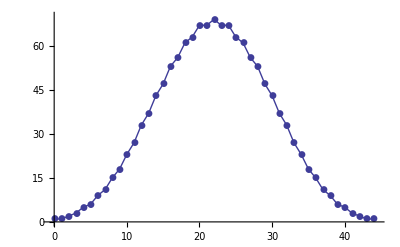

{1,1,2,3,5,6,9,11,15,18,23,27,33,37,43,47,53,56,61,63,67,67,69,67,67,63,61,56,53,47,43,37,33,27,23,18,15,11,9,6,5,3,2,1,1}

{1,1,2,3,5,6,9,11,15,18,23,27,33,37,43,47,53,56,61,63,67,67,69,67,67,63,61,56,53,47,43,37,33,27,23,18,15,11,9,6,5,3,2,1,1}

```mathematica
{p,q}={15,4}

UnorderedPartitionedPermutations[Range[p],{p-q,q}];
IndexList@@Range[p]/.(MapThread[Rule,{Flatten[#],Range[p]}]&/@%);
doperm/@%;
Tally[Last/@%];
ListPlot[%,Joined->True,PlotRange->{{-1/2,First@Last@%+1/2},{0,Max[Last/@%]+1}},PlotMarkers->Automatic]
Last/@%%
CoefficientList[Series[QBinomial[p,q,x],{x,0,100}],x]
```

```mathematica
generatePerms[partition:List[__Integer]]:=
Times@@(partition!)/Total[partition]! Plus@@(IndexList@@Range@Total@partition/.(MapThread[Rule,{Flatten[#],Range@Total@partition}]&/@UnorderedPartitionedPermutations[Range@Total@partition,partition]))

generatePerms[{1,2}]
```

1/3 ({1, 2, 3}+{2, 1, 3}+{2, 3, 1})

```mathematica
ClearAll[doCommute]
ClearAll[doCommute1]
ClearAll[doCommute2]

doCommute[perm:IndexList[integers__Integer],offset_Integer:0]:=
doCommute2[perm,doCommute1[IndexList[integers],#-1]&/@Range[Length@perm-1],offset];

doCommute[x_,offset_Integer:0]:=
x;

doCommute1[
perm:IndexList[before___Integer,x_Integer,y_Integer,after___Integer],
start_Integer
]/;x>y&&Length@{before}===start:=
IndexList[before,y,x,after]+IndexList[before,{x,y},after]

doCommute1[
perm:IndexList[before___Integer,x_Integer,y_Integer,after___Integer],
start_Integer
]/;x≤y&&Length@{before}===start:=Sequence[]

doCommute2[orig_IndexList,{},_]:=
orig;

doCommute2[_,{commutator_},_]:=
commutator

doCommute2[_,commutators_List,offset_Integer]:=
Module[{
constants=C[offset,#]&/@Range[Length@commutators-1]
},
Flatten[{1-Total[constants],constants}].commutators
];


doCommute[IndexList[2,1,6,3,4,5,7,1]]
doCommute[IndexList[1,2,3,5,4]]
doCommute[IndexList[2,1]]
```

(1-C[0,1]-C[0,2]) ({{2,1}, 6, 3, 4, 5, 7, 1}+{1, 2, 6, 3, 4, 5, 7, 1})+C[0,1] ({2, 1, {6,3}, 4, 5, 7, 1}+{2, 1, 3, 6, 4, 5, 7, 1})+C[0,2] ({2, 1, 6, 3, 4, 5, {7,1}}+{2, 1, 6, 3, 4, 5, 1, 7})

{1, 2, 3, {5,4}}+{1, 2, 3, 4, 5}

{, {2,1}}+{1, 2}

```mathematica
generateCommPerms[partition_]:=
Module[{
i=0,perms=generatePerms[partition],permlist
},
permlist=First/@Reverse[SortBy[
doperm/@Union[Cases[perms,_IndexList,{0,∞},Heads->True]],
Last
]];
Fold[Collect[#1/.#2:>doCommute[#2,i++],HoldPattern[IndexList[___]],Simplify]&,perms,permlist]
];
```

```mathematica
(aaaa #)&/@generateCommPerms[{3,1}];
List@@%/.x___*y_IndexList*z___:>{y,Times[x,z]}/.aaaa->1;
SortBy[%,Position[#,{_,_}]&]//TableForm[#,TableSpacing->{2,2}]&
```

{1, 2, 3, 4} | 1
{{4,1}, 2, 3} | 1/4
{1, {4,2}, 3} | 1/2
{1, 2, {4,3}} | 3/4

```mathematica
Solve[1/6 (1+2 C[1,1])==1/3 (1-C[1,1]),{C[1,1]}]
```

{{C[1,1]→1/4}}

```mathematica
1/6 (3-2 C[1,1])+1/3 C[1,1]//Simplify
```

1/2

```mathematica
Solve[1/6 (3-2 C[1,1])==1/3 C[1,1],{C[1,1]}]
```

{}

```mathematica
Solve[1+(1+2 C[1,1]) C[2,1]==-(1+2 C[1,1]) (-1+C[2,1])==2 (1-C[1,1]),{C[1,1],C[2,1]}]
```

{{C[1,1]→1/3,C[2,1]→1/5}}

```mathematica
%1188/.%1190[[1]]/.C[5,1]->1/14//Simplify//TableForm[#,TableSpacing->{2,2}]&
```

{1, 2, 4, {5,3}} | 16/3
{1, 2, {4,3}, 5} | 9
{1, 4, 2, {5,3}} | 1/3
{1, 4, {5,2}, 3} | 7/3
{1, {4,2}, 3, 5} | 8/3
{1, {4,2}, 5, 3} | 13/3
{4, 1, 2, {5,3}} | 1/3
{4, 1, {5,2}, 3} | 2/3
{4, {5,1}, 2, 3} | 1
{{4,1}, 2, 3, 5} | 4/3
{{4,1}, 2, 5, 3} | 4/3
{{4,1}, 5, 2, 3} | 4/3
{1, 2, 3, 4, 5} | 10

#### Code

The user function.

```mathematica
ClearAll[SymmetrizeCovDs]

SymmetrizeCovDs::usage=
"SymmetrizeCovDs[expr] converts all covariant derivatives in expr into symmetrized covariant derivatives by commuting them. \
SymmetrizeCovDs[expr, cd] only convert the covariant derivative cd.";

SymmetrizeCovDs[expr_]:=
Fold[SymmetrizeCovDs[#1,#2]&,expr,$CovDs];

SymmetrizeCovDs[expr_,cd_?SymCovDQ]:=
expr//.p:HoldPattern[cd[__][cd[__][_]]]:>SymmetrizeCovDs1[p];

SymmetrizeCovDs[expr_,_]:=
expr;
```

The worker function.

```mathematica
ClearAll[SymmetrizeCovDs1]

(* Eating one derivative from the left. *)
SymmetrizeCovDs1[HoldPattern[cd_[a_][cd_[inds__][expr_]]]]:=
Module[
{
l = Length@{inds},
i
},
cd[inds,a][expr] - Sum[
(l+1-i)/(l+1)PartitionedSymmetrize[cd[#1]@CovDCommutator[cd[#3]@expr,{#2,a},cd]&,{inds},{i-1,1,l-i}]
,
{i,1,l}
]
];

(* Eating one derivative from the right. *)
SymmetrizeCovDs1[HoldPattern[cd_[inds__][cd_[a_][expr_]]]]:=
Module[
{
l = Length@{inds},
i
},
cd[inds,a][expr] - Sum[
i/(l+1)PartitionedSymmetrize[cd[#1]@CovDCommutator[cd[#3]@expr,{a,#2},cd]&,{inds},{i-1,1,l-i}]
,
{i,1,l}
]
];

(* General case: do a recursion. *)
SymmetrizeCovDs1[HoldPattern[cd_[inds1__][cd_[inds2__][x_]]]]/;Length@{inds1}>1&&Length@{inds2}>1:=
PartitionedSymmetrize[cd[#1]@SymmetrizeCovDs[cd[#2]@cd[inds2]@x,cd]&,{inds1},{Length@{inds1}-1,1}];
```

#### Tests

Test it.

```mathematica
CD[a]@T1[b]
%//SymmetrizeCovDs
```

▽^a T1 | b

▽^a T1 | b

```mathematica
CD[b]@CD[a]@T1[c]
%//SymmetrizeCovDs
%//ExpandSymCovDs//SortCovDs//ToCanonical
```

▽^b▽^a T1 | c

-1/2 R[▽] | b | a |   | c
  |   | d |   T1 | d
 +▽_^(ab)T1 | c

▽^b▽^a T1 | c

```mathematica
CD[a,b]@T1[c]
%//ExpandSymCovDs//SortCovDs//ToCanonical
%//SymmetrizeCovDs//ToCanonical
```

▽_^(ab)T1 | c

1/2 R[▽] | a | b | c |  
  |   |   | d T1 | d
 +▽^b▽^a T1 | c

▽_^(ab)T1 | c

```mathematica
CD[c]@CD[b]@CD[a]@T1[d]
%//SymmetrizeCovDs//ToCanonical
%//ExpandSymCovDs//SortCovDs//ToCanonical
```

▽^c▽^b▽^a T1 | d

-1/2 R[▽] | b | c | d | e
  |   |   |   (▽^a T1 |  
e)-1/3 T1 | e
  (▽^b R[▽] | a | c | d |  
  |   |   | e)-1/2 R[▽] | a | c | d | e
  |   |   |   (▽^b T1 |  
e)-1/3 T1 | e
  (▽^c R[▽] | a | b | d |  
  |   |   | e)-1/2 R[▽] | a | b | d | e
  |   |   |   (▽^c T1 |  
e)-1/6 R[▽] | a | b | c | e
  |   |   |   (▽_e T1 | d
 )-1/6 R[▽] | a | c | b | e
  |   |   |   (▽_e T1 | d
 )-1/2 R[▽] | a | e | b | c
  |   |   |   (▽_e T1 | d
 )+▽_^(abc)T1 | d

▽^c▽^b▽^a T1 | d

```mathematica
CD[a]@CD[c,d]@T1[e]
%//SymmetrizeCovDs//ToCanonical
%%//ExpandSymCovDs//SortCovDs//ToCanonical
%%//ExpandSymCovDs//SortCovDs//ToCanonical
%%-%//ToCanonical
```

▽^a▽_^(cd)T1 | e

1/3 R[▽] | a | c | d | b
  |   |   |   (▽_b T1 | e
 )+1/3 R[▽] | a | d | c | b
  |   |   |   (▽_b T1 | e
 )+1/6 T1 | b
  (▽^c R[▽] | a | d | e |  
  |   |   | b)+1/2 R[▽] | a | d | e | b
  |   |   |   (▽^c T1 |  
b)+1/6 T1 | b
  (▽^d R[▽] | a | c | e |  
  |   |   | b)+1/2 R[▽] | a | c | e | b
  |   |   |   (▽^d T1 |  
b)+▽_^(acd)T1 | e

1/2 R[▽] | c | d | e | b
  |   |   |   (▽^a T1 |  
b)+1/2 R[▽] | a | b | c | d
  |   |   |   (▽_b T1 | e
 )+1/2 R[▽] | a | c | d | b
  |   |   |   (▽_b T1 | e
 )+1/2 R[▽] | a | d | c | b
  |   |   |   (▽_b T1 | e
 )+1/2 T1 | b
  (▽^c R[▽] | a | d | e |  
  |   |   | b)+R[▽] | a | d | e | b
  |   |   |   (▽^c T1 |  
b)+1/2 T1 | b
  (▽^d R[▽] | a | c | e |  
  |   |   | b)+R[▽] | a | c | e | b
  |   |   |   (▽^d T1 |  
b)+▽^d▽^c▽^a T1 | e

1/2 R[▽] | c | d | e | b
  |   |   |   (▽^a T1 |  
b)+1/2 R[▽] | a | b | c | d
  |   |   |   (▽_b T1 | e
 )+1/2 R[▽] | a | c | d | b
  |   |   |   (▽_b T1 | e
 )+1/2 R[▽] | a | d | c | b
  |   |   |   (▽_b T1 | e
 )+1/2 T1 | b
  (▽^c R[▽] | a | d | e |  
  |   |   | b)+R[▽] | a | d | e | b
  |   |   |   (▽^c T1 |  
b)+1/2 T1 | b
  (▽^d R[▽] | a | c | e |  
  |   |   | b)+R[▽] | a | c | e | b
  |   |   |   (▽^d T1 |  
b)+▽^d▽^c▽^a T1 | e

0

```mathematica
CD[c]@CD[b]@CD[a]@T1[d]
%//SymmetrizeCovDs//ToCanonical
%//ExpandSymCovDs//SortCovDs//ToCanonical
```

▽^c▽^b▽^a T1 | d

-1/2 R[▽] | b | c | d | e
  |   |   |   (▽^a T1 |  
e)-1/3 T1 | e
  (▽^b R[▽] | a | c | d |  
  |   |   | e)-1/2 R[▽] | a | c | d | e
  |   |   |   (▽^b T1 |  
e)-1/3 T1 | e
  (▽^c R[▽] | a | b | d |  
  |   |   | e)-1/2 R[▽] | a | b | d | e
  |   |   |   (▽^c T1 |  
e)-1/6 R[▽] | a | b | c | e
  |   |   |   (▽_e T1 | d
 )-1/6 R[▽] | a | c | b | e
  |   |   |   (▽_e T1 | d
 )-1/2 R[▽] | a | e | b | c
  |   |   |   (▽_e T1 | d
 )+▽_^(abc)T1 | d

▽^c▽^b▽^a T1 | d

```mathematica
CD[d]@CD[c]@CD[b]@CD[a]@T1[e]
%//SymmetrizeCovDs//ToCanonical
%//ExpandSymCovDs//SortCovDs//ToCanonical
```

▽^d▽^c▽^b▽^a T1 | e

1/12 R[▽] | a |   | e |  
  | g |   | f R[▽] | b | c | d | g
  |   |   |   T1 | f
 -1/4 R[▽] | a | d |   |  
  |   | f | g R[▽] | b | c | e | g
  |   |   |   T1 | f
 +1/12 R[▽] | a |   | e |  
  | g |   | f R[▽] | b | d | c | g
  |   |   |   T1 | f
 -1/4 R[▽] | a | c |   |  
  |   | f | g R[▽] | b | d | e | g
  |   |   |   T1 | f
 -1/24 R[▽] | a | c | d | g
  |   |   |   R[▽] | b |   | e |  
  | g |   | f T1 | f
 -1/24 R[▽] | a | d | c | g
  |   |   |   R[▽] | b |   | e |  
  | g |   | f T1 | f
 -1/4 R[▽] | a | g | c | d
  |   |   |   R[▽] | b |   | e |  
  | g |   | f T1 | f
 +1/4 R[▽] | a |   | e |  
  | g |   | f R[▽] | b | g | c | d
  |   |   |   T1 | f
 -1/4 R[▽] | a | b |   |  
  |   | f | g R[▽] | c | d | e | g
  |   |   |   T1 | f
 -1/24 R[▽] | a | b | d | g
  |   |   |   R[▽] | c |   | e |  
  | g |   | f T1 | f
 -1/24 R[▽] | a | d | b | g
  |   |   |   R[▽] | c |   | e |  
  | g |   | f T1 | f
 -1/4 R[▽] | a | g | b | d
  |   |   |   R[▽] | c |   | e |  
  | g |   | f T1 | f
 -1/24 R[▽] | a | b | c | g
  |   |   |   R[▽] | d |   | e |  
  | g |   | f T1 | f
 -1/24 R[▽] | a | c | b | g
  |   |   |   R[▽] | d |   | e |  
  | g |   | f T1 | f
 -1/4 R[▽] | a | g | b | c
  |   |   |   R[▽] | d |   | e |  
  | g |   | f T1 | f
 -1/3 (▽^b T1 | f
 ) (▽^c R[▽] | a | d | e |  
  |   |   | f)-1/3 (▽^a T1 | f
 ) (▽^c R[▽] | b | d | e |  
  |   |   | f)-1/3 (▽^b R[▽] | a | d | e |  
  |   |   | f) (▽^c T1 | f
 )-1/3 (▽^c T1 | f
 ) (▽^d R[▽] | a | b | e |  
  |   |   | f)-1/3 (▽^b T1 | f
 ) (▽^d R[▽] | a | c | e |  
  |   |   | f)-1/3 (▽^a T1 | f
 ) (▽^d R[▽] | b | c | e |  
  |   |   | f)-1/3 (▽^b R[▽] | a | c | e |  
  |   |   | f) (▽^d T1 | f
 )-1/3 (▽^c R[▽] | a | b | e |  
  |   |   | f) (▽^d T1 | f
 )-1/12 (▽^b R[▽] | a | c | d |  
  |   |   | f) (▽^f T1 | e
 )-1/12 (▽^b R[▽] | a | d | c |  
  |   |   | f) (▽^f T1 | e
 )-1/12 (▽^c R[▽] | a | b | d |  
  |   |   | f) (▽^f T1 | e
 )-1/12 (▽^c R[▽] | a | d | b |  
  |   |   | f) (▽^f T1 | e
 )-1/3 (▽^c R[▽] | a |   | b | d
  | f |   |  ) (▽^f T1 | e
 )-1/12 (▽^d R[▽] | a | b | c |  
  |   |   | f) (▽^f T1 | e
 )-1/12 (▽^d R[▽] | a | c | b |  
  |   |   | f) (▽^f T1 | e
 )-1/3 (▽^d R[▽] | a |   | b | c
  | f |   |  ) (▽^f T1 | e
 )-1/2 R[▽] | c | d | e | f
  |   |   |   (▽_^(ab)T1 |  
f)-1/2 R[▽] | b | d | e | f
  |   |   |   (▽_^(ac)T1 |  
f)-1/2 R[▽] | b | c | e | f
  |   |   |   (▽_^(ad)T1 |  
f)-1/6 R[▽] | b | c | d | f
  |   |   |   (▽_(f))^((a)T1 | e
 )-1/6 R[▽] | b | d | c | f
  |   |   |   (▽_(f))^((a)T1 | e
 )-1/2 R[▽] | b | f | c | d
  |   |   |   (▽_(f))^((a)T1 | e
 )-1/4 T1 | f
  (▽_^(bc)R[▽] | a | d | e |  
  |   |   | f)-1/2 R[▽] | a | d | e | f
  |   |   |   (▽_^(bc)T1 |  
f)-1/4 T1 | f
  (▽_^(bd)R[▽] | a | c | e |  
  |   |   | f)-1/2 R[▽] | a | c | e | f
  |   |   |   (▽_^(bd)T1 |  
f)-1/6 R[▽] | a | c | d | f
  |   |   |   (▽_(f))^((b)T1 | e
 )-1/6 R[▽] | a | d | c | f
  |   |   |   (▽_(f))^((b)T1 | e
 )-1/2 R[▽] | a | f | c | d
  |   |   |   (▽_(f))^((b)T1 | e
 )-1/4 T1 | f
  (▽_^(cd)R[▽] | a | b | e |  
  |   |   | f)-1/2 R[▽] | a | b | e | f
  |   |   |   (▽_^(cd)T1 |  
f)-1/6 R[▽] | a | b | d | f
  |   |   |   (▽_(f))^((c)T1 | e
 )-1/6 R[▽] | a | d | b | f
  |   |   |   (▽_(f))^((c)T1 | e
 )-1/2 R[▽] | a | f | b | d
  |   |   |   (▽_(f))^((c)T1 | e
 )-1/6 R[▽] | a | b | c | f
  |   |   |   (▽_(f))^((d)T1 | e
 )-1/6 R[▽] | a | c | b | f
  |   |   |   (▽_(f))^((d)T1 | e
 )-1/2 R[▽] | a | f | b | c
  |   |   |   (▽_(f))^((d)T1 | e
 )+▽_^(abcd)T1 | e

▽^d▽^c▽^b▽^a T1 | e

```mathematica
CD[a,b,c]@RicciCD[f,g]
%//ExpandSymCovDs//Expand;
%//SymmetrizeCovDs//ToCanonical
```

▽_^(abc)R[▽] | f | g
  |

▽_^(abc)R[▽] | f | g
  |

```mathematica
CD[a,b,c,d]@RicciCD[f,g]
%//ExpandSymCovDs//Expand;
%//SymmetrizeCovDs//ToCanonical
```

▽_^(abcd)R[▽] | f | g
  |

▽_^(abcd)R[▽] | f | g
  |

```mathematica
CD[a,b,c,d,e]@T1[f]
%//ExpandSymCovDs//Expand;
%//SymmetrizeCovDs//ToCanonical
```

▽_^(abcde)T1 | f

$Aborted

### VarD

#### Code

```mathematica
VarD[tensor_,covd_][covd_?SymCovDQ[inds__][expr_],rest_]:=(-1)^Length[{inds}]VarD[tensor,covd][expr,covd[inds][rest]]
```

#### Tests

```mathematica
VarD[T1[a],CD][T1[a]CD[-a,c]@T1[-c]]//CollectTensors
```

2 (▽_(ab)^T1 | b
 )

```mathematica
VarD[T1[a],CD][T1[a]CD[-a,c,d]@T2[-c,-d]]//CollectTensors
```

▽_(abc)^T2 | b | c
  |

```mathematica
VarD[T2[a,b],CD][T1[a]CD[-a,c,d]@T2[-c,-d]]//CollectTensors
```

-(▽_(abc)^T1 | c
 )

### ChangeCovD

#### Code

We simply expand all symmetrized covds before changing. Perhaps not efficient when covd2 is also symmetrizable, but it is simple.

```mathematica
Unprotect[ChangeCovD];

ChangeCovD[expr_,covd_?CovDQ,covd2_:PD]:=
If[xAct`xTensor`Private`CompatibleCovDsQ[covd,covd2],xAct`xTensor`Private`changeCovD[ExpandSymCovDs[expr,covd],covd,covd2,xAct`xTensor`Private`Identity1,Identity],expr];

Protect[ChangeCovD];
```

#### Tests

```mathematica
ChangeCovD[CD[a]@T1[b]]
```

Γ[▽] | b | a |  
  |   | c T1 | c
 +∂^a T1 | b

```mathematica
ChangeCovD[CD[a,c]@T1[b]]
%-ChangeCovD[1/2(CD[a]@CD[c]@T1[b] + CD[c]@CD[a]@T1[b])]//ToCanonical
```

1/2 (T1 | d
  ∂^a Γ[▽] | b | c |  
  |   | d+Γ[▽] | b | c |  
  |   | d ∂^a T1 | d
 +Γ[▽] | b | c |  
  |   | i (Γ[▽] | i | a |  
  |   | g T1 | g
 +∂^a T1 | i
 )+∂^a ∂^c T1 | b
 +T1 | g
  ∂^c Γ[▽] | b | a |  
  |   | g+Γ[▽] | b | a |  
  |   | e (Γ[▽] | e | c |  
  |   | d T1 | d
 +∂^c T1 | e
 )+Γ[▽] | b | a |  
  |   | g ∂^c T1 | g
 +∂^c ∂^a T1 | b
 +Γ[▽] | c | a |  
  |   | f (Γ[▽] | b | f |  
  |   | d T1 | d
 +∂^f T1 | b
 )+Γ[▽] | a | c |  
  |   | h (Γ[▽] | b | h |  
  |   | g T1 | g
 +∂^h T1 | b
 ))

0

### ContractMetric

#### Code

This is a simple modification of xTensor’s ContractMetric1. It currently ignores OverDerivatives and only contracts when the derivative is metric compatible.

```mathematica
(CM:xAct`xTensor`Private`ContractMetric1[{od_,aud_},{metric_,nv_}])[rest_. der_?SymCovDQ[inds__][expr_]met:metric_[b_,c_]]:=
Module[{dm=der[inds][met],result},
If[(dm===0)&&xAct`xTensor`Private`differentexpressionsQ[result=CM[expr met],{expr,met}],
CM[rest der[inds][result]],
CM[rest met]der[inds][expr]]
]/;(MemberQ[FindFreeIndices[expr],ChangeIndex[c]|ChangeIndex[b]]&&Head[expr]=!=metric);
```

#### Tests

```mathematica
CD[a,b]@RiemannCD[c,d,e,f]
metric[-d,-f]%//ContractMetric//ToCanonical
metric[-a,-b]%%//ContractMetric//ToCanonical
metric[-a,-c]%%%//ContractMetric//ToCanonical
metric[-b,-c]%%%%//ContractMetric//ToCanonical
```

▽_^(ab)R[▽] | c | d | e | f
  |   |   |

▽_^(ab)R[▽] | c | e
  |

▽_(a))^((a)R[▽] | c | d | e | f
  |   |   |

-(▽_(c))^((b)R[▽] | d | c | e | f
  |   |   |  )

-(▽_(c))^((a)R[▽] | d | c | e | f
  |   |   |  )

### Perturbations

#### Code

We simply expand any symmetric covds inside Perturbations. This is the simplest approach, but not the most efficient. Ideally Perturbation should not expand symcovds; only xAct`xPert`ExpandPerturbationDer should.

```mathematica
Unprotect[Perturbation];

HoldPattern[Perturbation[p_,n_.]]/;!FreeQ[p,_?SymCovDQ[inds__][_]/;Length@{inds}>1]:=Perturbation[ExpandSymCovDs[p],n]

Protect[Perturbation];
```

#### Tests

```mathematica
Perturbation[CD[d]@CD[a,b]@T1[c]]
```

1/2 (△[▽^d▽^a▽^b T1 | c
 ]+△[▽^d▽^b▽^a T1 | c
 ])

```mathematica
Perturbation[CD[a,b]@RicciScalarCD[]]
```

1/2 (△[▽^a▽^b R[▽]]+△[▽^b▽^a R[▽]])

### Timings

#### Eating one derivative on the right

```mathematica
CD[a]@CD[b]@S3[g,h,i]
time[1]=%//SymmetrizeCovDs//ToCanonical//AbsoluteTiming//First
```

▽^a▽^b S3 | g | h | i
  |   |

0.02584

```mathematica
CD[a]@CD[b,c]@S3[g,h,i]
time[2]=%//SymmetrizeCovDs//ToCanonical//AbsoluteTiming//First
```

▽^a▽_^(bc)S3 | g | h | i
  |   |

0.14113

```mathematica
CD[a]@CD[b,c,d]@S3[g,h,i]
time[3]=%//SymmetrizeCovDs//ToCanonical//AbsoluteTiming//First
```

▽^a▽_^(bcd)S3 | g | h | i
  |   |

1.34065

```mathematica
CD[a]@CD[b,c,d,e]@S3[g,h,i]
time[4]=%//SymmetrizeCovDs//ToCanonical//AbsoluteTiming//First
```

▽^a▽_^(bcde)S3 | g | h | i
  |   |

18.53713

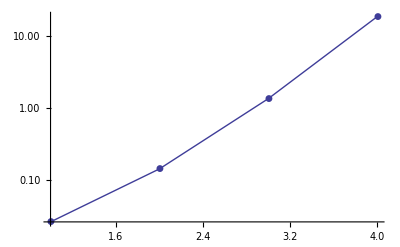

```mathematica
ListLogPlot[Table[{i,time[i]},{i,4}],Joined->True,PlotMarkers->Automatic]
```

#### Eating one derivative on the left

```mathematica
CD[a]@CD[b]@S3[g,h,i]
time[1]=%//SymmetrizeCovDs//ToCanonical//AbsoluteTiming//First
```

▽^a▽^b S3 | g | h | i
  |   |

0.02584

```mathematica
CD[b,c]@CD[a]@S3[g,h,i]
time[2]=%//SymmetrizeCovDs//ToCanonical//AbsoluteTiming//First
```

▽_^(bc)▽^a S3 | g | h | i
  |   |

0.14037

```mathematica
CD[b,c,d]@CD[a]@S3[g,h,i]
time[3]=%//SymmetrizeCovDs//ToCanonical//AbsoluteTiming//First
```

▽_^(bcd)▽^a S3 | g | h | i
  |   |

1.38543

```mathematica
CD[b,c,d,e]@CD[a]@S3[g,h,i]
time[4]=%//SymmetrizeCovDs//ToCanonical//AbsoluteTiming//First
```

▽_^(bcde)▽^a S3 | g | h | i
  |   |

18.4137

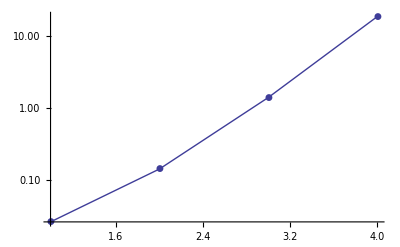

```mathematica
ListLogPlot[Table[{i,time[i]},{i,4}],Joined->True,PlotMarkers->Automatic]
```